```mathematica
Table[Factor[ChromaticPolynomial[JacobsThalGraph2[k],x]],{k,10}]
```

{x,(-1+x) x,(-2+x) (-1+x) x,(-3+x) (-2+x) (-1+x) x,(-3+x)^2 (-2+x) (-1+x) x,(-2+x) (-1+x) x (-32+29 x-9 x^2+x^3),(-3+x) (-2+x) (-1+x) x (-35+30 x-9 x^2+x^3),(-2+x) (-1+x) x (-332+498 x-303 x^2+94 x^3-15 x^4+x^5),(-3+x) (-2+x) (-1+x) x (7-5 x+x^2) (-49+38 x-10 x^2+x^3),(-2+x) (-1+x) x (-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7)}

```mathematica
CoefficientList[-3152+6787 x-6301 x^2+3269 x^3-1025 x^4+195 x^5-21 x^6+x^7,x]//Abs//Reverse
```

{1,21,195,1025,3269,6301,6787,3152}

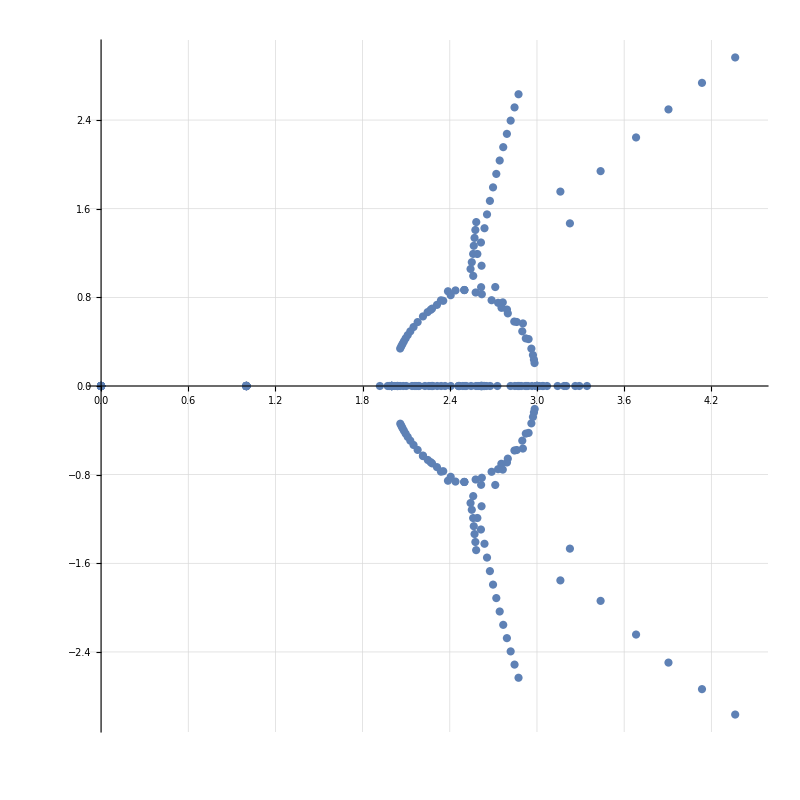

```mathematica
Monitor[ListPlot[Flatten[Table[Map[ReIm,ComplexExpand[x/.NSolve[ChromaticPolynomial[JacobsThalGraph2[k],x]==0,x]]],{k,25}],1],
GridLines->Automatic,  PlotRangeClipping->True, ImageSize->800, AspectRatio->1],k]
```

```mathematica
LegendreBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = LegendreP[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

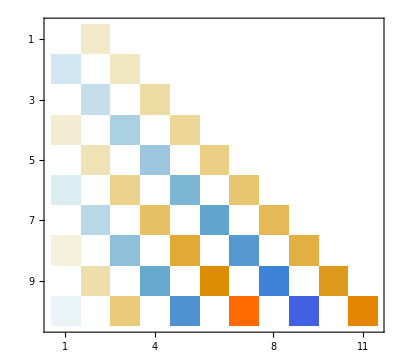

```mathematica
Table[CoefficientList[LegendreP[pos,x],x],{pos,10}]//MatrixPlot
```

```mathematica
LegendreBaseCoeff[x^7-1]
```

{-1,1/3,0,14/33,0,8/39,0,16/429}

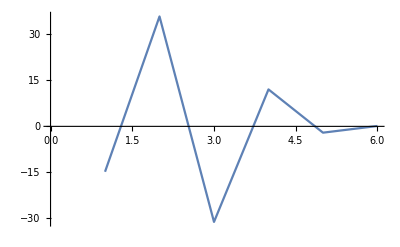
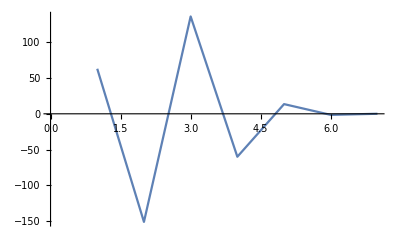
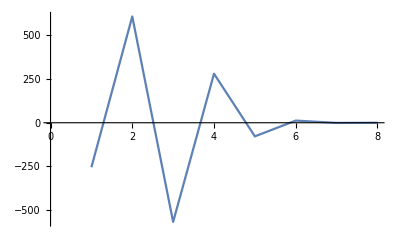
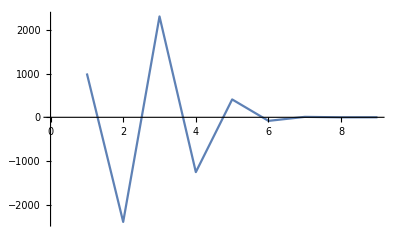
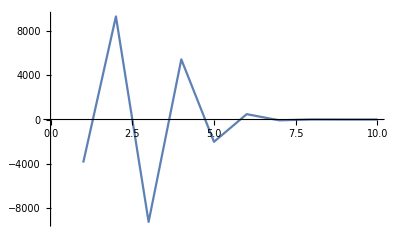
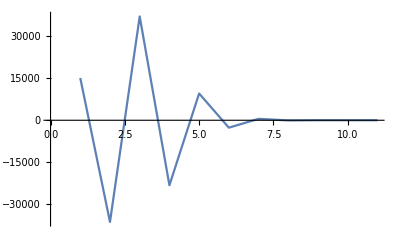
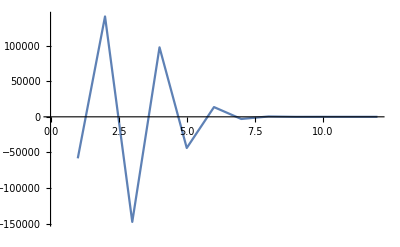
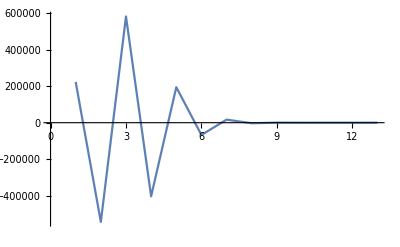

```mathematica
Map[ListLinePlot,Table[LegendreBaseCoeff[ChromaticPolynomial[JacobsThalGraph[k],x]],{k,10}]]
```

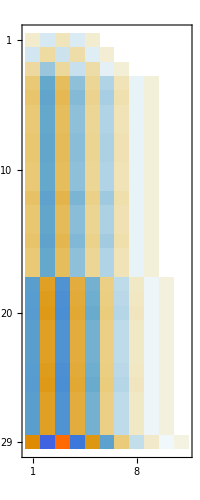

```mathematica
Table[LegendreBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]],{k,Select[Range[100],FileExistsQ[RootGrofsPath <> ToString[#] <> ".grof"]&]}]//MatrixPlot
```

```mathematica
JacobiBaseCoeff[p_,a_,b_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = JacobiP[pos,a,b,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
HermiteBaseCoeff[p_]:=Block[
{result={},degree=Exponent[p,x],pos,current,temp,cof,poly=p},
For[pos=degree,pos≥1,pos--,
current = HermiteH[pos,x];
temp=Factor[poly-a*current];
cof=First[a/.Solve[Coefficient[temp,x^pos]==0,a]];
result=Append[result,cof];
poly=FullSimplify[poly-cof*current]
];
result=Append[result,poly];
Reverse[result]
]
```

```mathematica
Table[HermiteBaseCoeff[ChromaticPolynomial[ReadGrof[k],x]],{k,Select[Range[100],FileExistsQ[RootGrofsPath <> ToString[#] <> ".grof"]&]}]//MatrixForm
```

({25/4,-15/2,7/2,-3/4,1/16}
{-105/4,261/8,-33/2,17/4,-9/16,1/32}
{891/8,-144,1257/16,-93/4,127/32,-3/8,1/64}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{38193/16,-13311/4,16389/8,-11689/16,5313/32,-397/16,77/32,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{36411/16,-12735/4,31521/16,-11317/16,2593/16,-391/16,153/64,-9/64,1/256}
{36411/16,-12735/4,31521/16,-11317/16,2593/16,-391/16,153/64,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{40715/16,-7059/2,34507/16,-12185/16,2737/16,-101/4,155/64,-9/64,1/256}
{36411/16,-12735/4,31521/16,-11317/16,2593/16,-391/16,153/64,-9/64,1/256}
{36411/16,-12735/4,31521/16,-11317/16,2593/16,-391/16,153/64,-9/64,1/256}
{39411/16,-13709/4,33663/16,-11959/16,2705/16,-201/8,155/64,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{33267/16,-23427/8,29271/16,-10641/16,2475/16,-759/32,151/64,-9/64,1/256}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-160173/16,468135/32,-9624,120167/32,-30785/32,2699/16,-163/8,211/128,-21/256,1/512}
{-167823/16,488769/32,-160023/16,31041/8,-15799/16,11001/64,-1319/64,53/32,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-160173/16,468135/32,-9624,120167/32,-30785/32,2699/16,-163/8,211/128,-21/256,1/512}
{-167823/16,488769/32,-160023/16,31041/8,-15799/16,11001/64,-1319/64,53/32,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{-146655/16,431475/32,-143163/16,112917/32,-14643/16,5205/32,-1275/64,209/128,-21/256,1/512}
{1495707/32,-1137111/16,3154029/64,-658907/32,368757/64,-72515/64,20399/128,-2039/128,559/512,-3/64,1/1024})

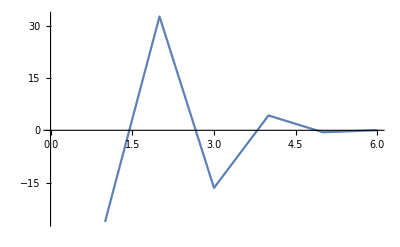
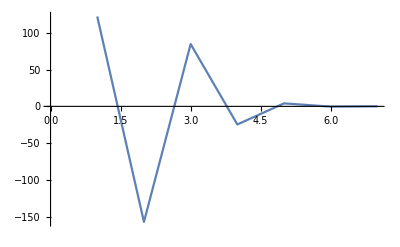
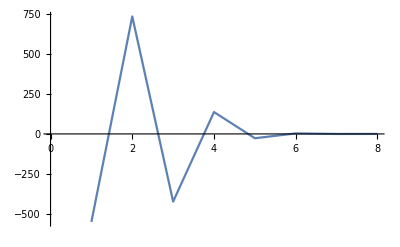
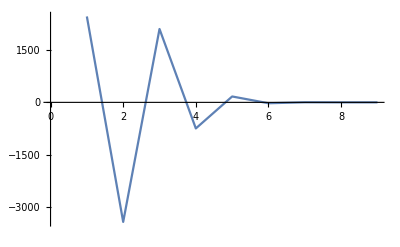
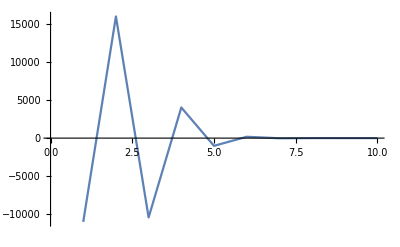
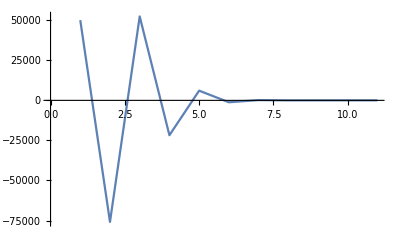
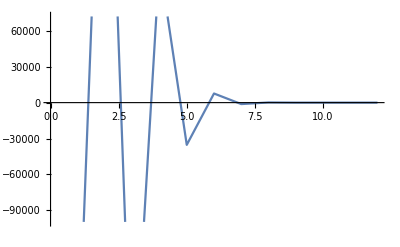
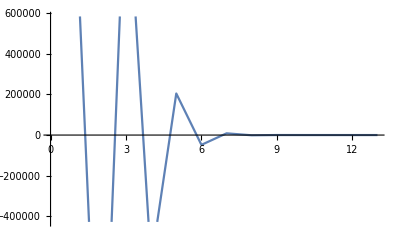

```mathematica
Map[ListLinePlot,Table[HermiteBaseCoeff[ChromaticPolynomial[JacobsThalGraph[k],x]],{k,10}]]
```